```mathematica
Fitn[q_,nu_,qq_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qq]]/( BesselI[0,1/nu]),1];
```

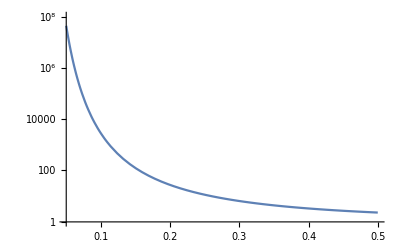

```mathematica
f1 =LogPlot[BesselI[0,1/x],{x,0.05,0.5},PlotRange->All]
```

```mathematica
varfitn = Table[Fitn[q,nu,0.5],{nu,0.01,2,0.05},{q,0,1,0.005}];
```

```mathematica
vf = Map[Variance,varfitn];
```

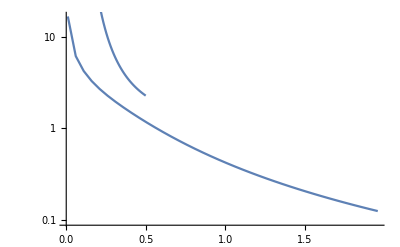

```mathematica
data2 ={Range[0.01,2,0.05],vf}//Transpose;
Show[ListLogPlot[data2,Joined->True],f1]
```

```mathematica
localfolder = "C:\\Users\\tramiada\\OneDrive\\Projects\\et3\\sim1\\";
```

```mathematica
RES= {};
Do[
result= {};
Do[
repl= {};
Do[data = Import[localfolder<>"sim_est_z_1_aggreg_"<>ToString@agg<>"_M_1_com_id_"<>ToString@id<>"_size_12_T_4000_muR_0.1_lambda_0.2_gH_1_replicates_"<>ToString@rep<>".csv"];
temp = data[[-3]]; (* -1 is time, -2 is empty*)
AppendTo[repl,{ NU[[id+1]],If[temp[[1]]==100,Infinity,π temp[[2]]^2  temp[[1]] temp[[3]]]}];
,{rep,0,9,1}];
AppendTo[result,repl];
,{id,0,29,1}];
mean2 = Map[Mean,result];
AppendTo[RES,mean2];
,{agg,{0}}];
```

```mathematica
RES[[1]]
```

{{0.002,0.432283},{0.0027,0.405894},{0.003645,0.42223},{0.00492075,0.398354},{0.00664301,0.388301},{0.00896807,0.361911},{0.0121069,0.335522},{0.0163443,0.344319},{0.0220648,0.310389},{0.0297875,0.277717},{0.0402131,0.316673},{0.0542877,0.282743},{0.0732884,0.271434},{0.0989393,0.245044},{0.133568,0.233734},{0.180317,0.216142},{0.243428,0.207345},{0.328628,0.177186},{0.443647,0.174673},{0.598924,0.15708},{0.808547,0.148283},{1.09154,0.148283},{1.47358,0.144513},{1.98933,0.140743},{2.68559,0.14577},{3.62555,0.139487},{4.8945,0.148283},{6.60757,0.13069},{8.92022,0.14577},{∞,0.147027}}

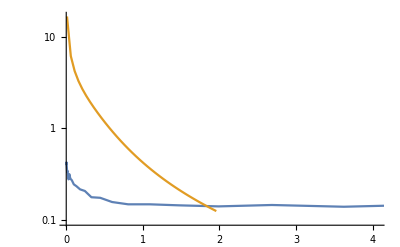

```mathematica
ListLogPlot[{RES[[1]],data2},Joined->True]
```

```mathematica
data
```

{{0.1,0.2,1,0},{0.2,0.2,1,0},{0.3,0.2,1,0},{0.4,0.2,1,0},{0.5,0.2,1,0},{0.6,0.2,1,0},{0.7,0.2,1,0},{0.8,0.2,1,0},{0.9,0.2,1,0},{1,0.2,1,0},{1.1,0.2,1,0.0846355},{},{321.564}}